```mathematica
(*tree16是所给的基础树, cycletree[p,v]Subscript[是在tree16的第v点上挂上一个C, p].A是取邻接矩阵,DMat是度数对角阵*)
tree16=EdgeAdd[PathGraph[Range[10]],{3<->11,11<->12,6<->13,13<->14,14<->15,9<->16}];
cycletree[p_Integer,v_]:=GraphUnion[tree16,Graph[Join[{v<->17,15+p<->v},Table[16+k<->17+k,{k,1,p-2}]]]];
A[G_Graph]:=Normal[AdjacencyMatrix[G]];
DMat[G_Graph]:=DiagonalMatrix@VertexDegree[G];
ψ[G_Graph,t_,μ_]:=Det[t IdentityMatrix[VertexCount[G]]-AdjacencyMatrix[G]+μ DMat[G]];
```

```mathematica
(*用函数FindDegSimMat来寻找G1和G2之间是否度相似,若否则函数输出的Det为0.*)
FindDegSimMat[G1_Graph,G2_Graph]:=Module[{n=VertexCount[G1],M},If[n!=VertexCount[G2],Abort[]];M=Array[Subscript[m, #1,#2]&,{n,n}];M=M/.Solve[{A[G1].M==M.A[G2],DMat[G1].M==M.DMat[G2]}][[1]]];
tree16DegSimMat[p_Integer,v1_,v2_]:=FindDegSimMat[cycletree[p,v1],cycletree[p,v2]];
```

```mathematica
(*例子: 一对度相似但不同构的图*)
Subscript[X, 1,1]=Graph[{1<->2,3<->4,5<->6,6<->7,7<->8,8<->9,1<->6,2<->7,3<->8,4<->9,1<->10,3<->10,1<->9,2<->5,2<->6,3<->7,4<->5,4<->8,5<->9}];
Subscript[X, 1,2]=Graph[{1<->2,1<->5,1<->7,1<->8,2<->8,2<->9,2<->10,3<->4,3<->5,3<->6,3<->9,4<->6,4<->7,4<->10,5<->6,5<->9,6<->7,7<->8,8<->9}];
FindDegSimMat[Subscript[X, 1,1],Subscript[X, 1,2]]//Det//FullSimplify
```

1024 m_(1,1)^9 (m_(1,1)+2 m_(2,1))

```mathematica
graphlist={{0<->11,0<->12,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->11,0<->12,1<->11,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->11,0<->12,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->11,0<->12,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->11,0<->12,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->11,0<->12,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->11,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->11,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->11,0<->12,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->11,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->11,0<->12,1<->11,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->11,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->11,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->11,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,0<->12,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->11,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,0<->11,0<->12,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,0<->11,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->11,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,0<->11,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->10,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->10,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12,11<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11},{0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11},{0<->10,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->10,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->10,0<->11,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->10,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->10,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->10,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->10,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->10,0<->12,1<->11,1<->12,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->12,1<->11,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->11,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->11,1<->11,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->12,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->12,1<->11,1<->12,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->11,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->10,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->10,0<->11,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->10,1<->10,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,11<->12},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->11,11<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->11,10<->12},{0<->9,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->11,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->10,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->10,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->11,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->10,1<->11,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->10,1<->11,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->10,1<->10,1<->11,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->10,1<->12,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->10,0<->12,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->11,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->10,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->10,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->11,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->10,1<->11,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->10,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->10,1<->11,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->10,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11},{0<->9,0<->12,1<->10,1<->12,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->11,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,1<->12,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->11,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12,10<->11},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,2<->12,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12,11<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,9<->12,10<->11},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,9<->11,10<->11},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->11},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->11},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->11},{0<->9,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,9<->12,10<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11,10<->11,11<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->10,2<->11,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->10,2<->11,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->10,2<->11,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->10,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->11,3<->10,4<->10,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,2<->12,3<->10,4<->10,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,3<->12,4<->10,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->10,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->10,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->10,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,3<->11,4<->10,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,3<->11,4<->10,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,4<->12,5<->11,6<->12,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->11,9<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->11,9<->12,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,9<->11,10<->12},{0<->9,1<->9,2<->10,2<->11,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,9<->11},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->12,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->11},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12,9<->11},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->11,10<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->11,9<->12,10<->12},{0<->9,1<->9,2<->10,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->11,9<->12,10<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->10,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->12,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->10,1<->9,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12,11<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,0<->11,1<->9,2<->10,3<->11,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->10,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->11,2<->10,2<->12,3<->11,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->10,1<->9,1<->12,2<->10,3<->11,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->11,2<->10,2<->12,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,4<->12,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->12,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->12,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12,10<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12,11<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,11<->12},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12,11<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12,11<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12,10<->12,11<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,1<->11,2<->10,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->12,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,3<->12,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12},{0<->9,0<->11,0<->12,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,1<->12,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12,9<->10,10<->12},{0<->9,0<->11,1<->9,2<->10,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->10,9<->12,10<->12},{0<->9,0<->12,1<->9,1<->12,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->10},{0<->9,0<->12,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->10},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12,9<->10},{0<->9,0<->12,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->10,9<->12},{0<->9,1<->9,2<->10,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->11,8<->12,9<->10,9<->12},{0<->9,1<->9,2<->10,3<->10,4<->11,4<->12,5<->11,5<->12,6<->11,7<->11,8<->12,9<->10,9<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,1<->12,2<->9,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,2<->9,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->10,2<->9,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->9,2<->11,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->9,2<->11,2<->12,3<->10,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->9,2<->11,3<->10,3<->12,4<->11,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->9,2<->11,3<->10,4<->11,4<->12,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->9,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->10,2<->9,2<->12,3<->10,4<->11,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->10,2<->9,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->10,2<->9,2<->12,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->10,2<->9,3<->10,4<->11,5<->11,6<->11,7<->12,8<->12,9<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->9,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,2<->12,3<->10,3<->11,4<->10,5<->11,6<->12,7<->12,8<->12},{0<->9,0<->10,0<->11,0<->12,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->9,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->9,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->11,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->9,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12},{0<->9,0<->10,0<->11,1<->9,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,1<->12,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->9,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->9,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,1<->12,2<->9,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,2<->12,3<->10,3<->12,4<->10,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,3<->10,3<->12,4<->10,4<->12,5<->11,6<->11,7<->12,8<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12},{0<->9,0<->10,0<->12,1<->9,1<->11,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,2<->12,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->12,8<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,9<->12,10<->12},{0<->9,0<->10,1<->9,1<->11,2<->9,3<->10,4<->10,5<->11,6<->11,7<->12,8<->12,10<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,2<->12,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12},{0<->9,0<->10,0<->12,1<->9,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->9,3<->10,3<->12,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,6<->12,7<->11,8<->12,9<->12},{0<->9,0<->10,1<->9,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12,10<->12},{0<->9,0<->10,0<->12,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,2<->12,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,11<->12},{0<->9,0<->10,0<->12,1<->9,2<->9,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,1<->12,2<->9,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->9,3<->10,3<->12,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->9,3<->10,4<->10,5<->11,5<->12,6<->11,7<->11,8<->12,9<->12,11<->12},{0<->9,0<->10,1<->9,2<->9,3<->10,4<->10,5<->11,6<->11,7<->11,8<->12,9<->12,10<->12,11<->12},{0<->9,0<->12,1<->9,1<->12,2<->9,3<->10,3<->12,4<->10,5<->10,6<->11,6<->12,7<->11,8<->11},{0<->9,0<->12,1<->9,2<->9,3<->10,3<->12,4<->10,5<->10,6<->11,6<->12,7<->11,8<->11,9<->12},{0<->9,1<->9,2<->9,3<->10,3<->12,4<->10,4<->12,5<->10,6<->11,6<->12,7<->11,8<->11,9<->12},{0<->9,0<->12,1<->9,2<->9,3<->10,4<->10,5<->10,6<->11,6<->12,7<->11,8<->11,9<->12,10<->12},{0<->9,1<->9,2<->9,3<->10,4<->10,5<->10,6<->11,6<->12,7<->11,7<->12,8<->11,9<->12,10<->12},{0<->9,0<->12,1<->9,2<->9,3<->10,4<->10,5<->10,6<->11,7<->11,8<->11,9<->12,10<->12,11<->12},{0<->8,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->8,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12},{0<->8,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->8,0<->11,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->8,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,9<->12},{0<->8,0<->11,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->12,5<->12,6<->12,7<->12,9<->12},{0<->8,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,4<->12,5<->12,6<->12,7<->12,11<->12},{0<->8,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,4<->12,5<->12,6<->12,7<->12},{0<->8,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,8<->12},{0<->8,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,3<->12,4<->11,5<->12,6<->12,7<->12,11<->12},{0<->8,0<->12,1<->9,1<->12,2<->10,2<->12,3<->11,4<->11,5<->12,6<->12,7<->12,8<->12,11<->12},{0<->8,0<->11,0<->12,1<->9,1<->12,2<->10,2<->12,3<->12,4<->12,5<->12,6<->12,7<->12,8<->11},{0<->8,0<->11,0<->12,1<->9,1<->11,1<->12,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12},{0<->8,0<->11,0<->12,1<->9,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->8,0<->11,1<->9,1<->11,1<->12,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12},{0<->8,0<->11,1<->9,1<->11,2<->10,2<->11,3<->12,4<->12,5<->12,6<->12,7<->12,8<->12,9<->12},{0<->8,0<->11,0<->12,1<->9,1<->11,2<->10,2<->11,3
```

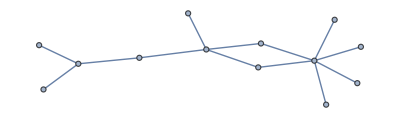
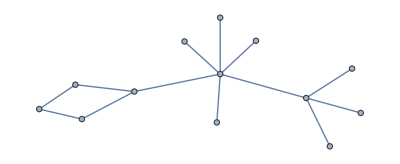
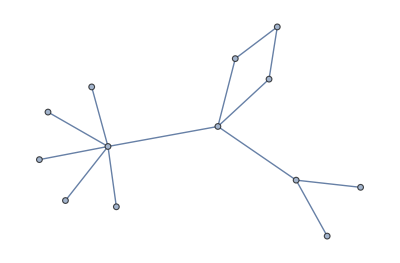
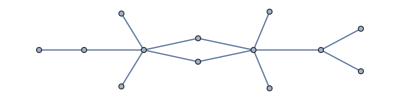
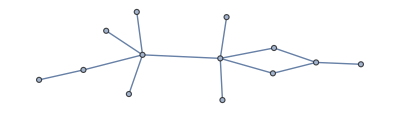
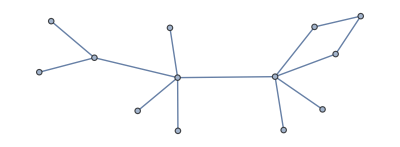
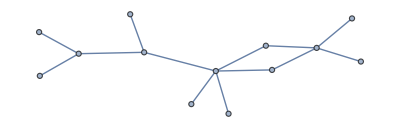
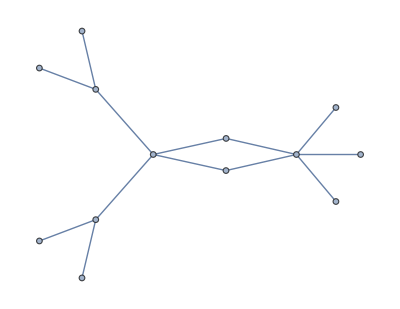
{0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Det[FindDegSimMat[-Graphics-,-Graphics-,-Graphics-]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Select[GatherBy[UnicyclicGraphList,{Sort@VertexDegree@#,CharacteristicPolynomial[AdjacencyMatrix@#,x]}&],Length[#]>1&];
Det/@(FindDegSimMat@@@%)
```